See Wald Eq. (6.3.35)

```mathematica
critSol=First@NDSolve[{1/r'[ϕ]==-L/r[ϕ]^2 1/(√(1-L^2(r[ϕ]-2)/r[ϕ]^3))/.L->√27,r[0]==50},r,{ϕ,0,4π}]
```

{r→InterpolatingFunction[…]}

```mathematica
Manipulate[PolarPlot[r[ϕ-δ]/.critSol,{ϕ,δ,4π+δ}],{δ,0,π}]
```

```mathematica
Δ=π/2+.1;
```

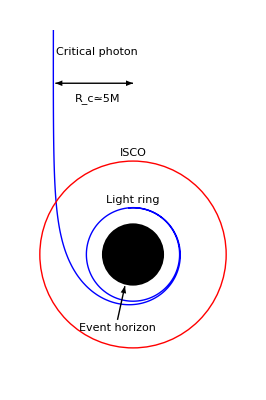

```mathematica
fig=Show[PolarPlot[r[ϕ-Δ]/.critSol,{ϕ,Δ,4π+Δ},PlotRange->{{-7,7},{-7,14}},Axes->False,PlotStyle->{Thick,Blue}],Graphics[{Disk[{0,0},2],Thick,Red,Circle[{0,0},6],
Black,FontSize->14,
Text["Event horizon",{-1,-4.7}],Arrow[{{-1,-4.2},2.1{Cos[θ],Sin[θ]}/.θ->1.42π}],
Text["Light ring", {0,3.5}],
(*Arrow[{{1,4.2},3.1{Cos[θ],Sin[θ]}/.θ->.42π}],*)
Text["ISCO",{0,6.5}],
Text["Critical photon",{-2.3,13}],
Arrowheads[{-.05,.05}],Arrow[{{-5,11},{0,11}}],
Text["R_c≃5M",{-2.3,10}]}]]
```

```mathematica
Export[NotebookDirectory[]<>"bh-dist-fig.pdf",fig]
```

/Users/leo/Documents/projects/eht-bh-fact-sheet/bh-dist-fig.pdf